## Definitions of Functions

```mathematica
(* load additional packages *)
<<"Combinatorica`"
<<"MultivariateStatistics`"

(* density of bivariate normal distribution *)
RNormalDens[x_,y_,mu_,Sigma_]:=ⅇ^(-1/2 {x-mu⟦1⟧,y-mu⟦2⟧}.Inverse[Sigma].{x-mu⟦1⟧,y-mu⟦2⟧})/(2 π √Det[Sigma]);

(* function for computing a 2x2 covariance matrix by rotating the diagonal matrix with entries (sx,sy) by an angle phi *)
RotateDiagonalCovarianceMatrix[sx_,sy_,phi_]:=Module[{T},T={{sx Cos[phi],-sy Sin[phi]},{sx Sin[phi],sy Cos[phi]}};Return[T.Transpose[T]]];

(* function for creating a data set consisting of n points according to a bivariate normal distribution with mean mu
	and covariance matrix Sigma; in the third component, a label class is added to all samples *)
CreateGaussBlob[n_,mu_,Sigma_,class_]:=Module[{i,input,SigmaSqrt,dataset={}},
SigmaSqrt=CholeskyDecomposition[Sigma];
For[i=1,i≤n,i++,
input=mu+{Random[NormalDistribution[0,1]],Random[NormalDistribution[0,1]]}.SigmaSqrt;
dataset=Append[dataset,Flatten[{input,class}]]];
Return[dataset]];

(* function that returns the optimal discriminate function for the case that both the negative and the positive class
	are bivariate normal distributions with parameters (nmu,nSigma) and (pmu,pSigma), respectively; the marginal
	probabilities of negative and positive class are supposed to be np and pp, respectively *)
TwoGaussDiscFunction[pp_,pmu_,pSigma_,np_,nmu_,nSigma_]:=(pp RNormalDens[#1,#2,pmu,pSigma]-np RNormalDens[#1,#2,nmu,nSigma])/(pp RNormalDens[#1,#2,pmu,pSigma]+np RNormalDens[#1,#2,nmu,nSigma])&;

(* function that draws a data set together with a discriminate function according to the above conventions *)
MakeGaussPlot[data_,pp_,pmu_,pSigma_,np_,nmu_,nSigma_]:=ShowClassification[{ClassificationFunctionPlot[TwoGaussDiscFunction[pp,pmu,pSigma,np,nmu,nSigma]],
ClassificationDataPlot[data]}];

(* function for estimating parameters of Gaussian distributions of negative and positive classes
	and drawing the discriminant function together with the data set *)
MakeGaussPlotEstimates[data_]:=Module[{neg,pos,pp,pmu,pSigma,np,nmu,nSigma},
neg=Select[data,#1⟦3⟧==-1&];
pos=Select[data,#1⟦3⟧==1&];
pp=Length[pos]/Length[data];
np=Length[neg]/Length[data];
pmu={Mean[pos[[All,1]]],Mean[pos[[All,2]]]};
nmu={Mean[neg[[All,1]]],Mean[neg[[All,2]]]};
pSigma=Covariance[pos[[All,1;;2]]];
nSigma=Covariance[neg[[All,1;;2]]];
Print["Negative class: no. of samples=",Length[neg]," mu=",nmu," Sigma=",nSigma];Print["Positive class: no. of samples=",Length[pos]," mu=",pmu," Sigma=",pSigma];
MakeGaussPlot[data,pp,pmu,pSigma,np,nmu,nSigma]];

(* auxiliary function for making some plots for a mixture of bivariate normal distributions:
	(1) marginal p(x);
	  (2) discriminant function g(x)=p(y=1|x)*p(y=1)-p(y=-1|x)*p(y=1-);
	  (3) discriminant function g(x)/p(x)
	plot ranges are adjusted specifically *)
MakeGaussDistributionPlots[pp_,pmu_,pSigma_,np_,nmu_,nSigma_]:=Module[{ppeak,npeak},
ppeak=pp RNormalDens[pmu⟦1⟧,pmu⟦2⟧,pmu,pSigma];
npeak=np RNormalDens[nmu⟦1⟧,nmu⟦2⟧,nmu,nSigma];
Show[GraphicsArray[{Plot3D[pp RNormalDens[x,y,pmu,pSigma]+np RNormalDens[x,y,nmu,nSigma],{x,-0.1,1.1},{y,-0.1,1.1},
PlotPoints->51,PlotRange->{0,Max[ppeak,npeak]}],
Plot3D[pp RNormalDens[x,y,pmu,pSigma]-np RNormalDens[x,y,nmu,nSigma],{x,-0.1,1.1},{y,-0.1,1.1},
PlotPoints->51,PlotRange->{-npeak,ppeak}],
Plot3D[TwoGaussDiscFunction[pp,pmu,pSigma,np,nmu,nSigma][x,y],{x,-0.1,1.1},{y,-0.1,1.1},
PlotPoints->51,PlotRange->{-1,1}]}],ImageSize->{700,Automatic}]];
```

## Example 1

Define distribution parameters and create data set:

```mathematica
pmu1={0.4,0.8};
pSigma1=RotateDiagonalCovarianceMatrix[0.3,0.07,0];
nmu1={0.5,0.3};
nSigma1=RotateDiagonalCovarianceMatrix[0.05,0.2,0.2];
GaussDataSet=Join[CreateGaussBlob[55,pmu1,pSigma1,1],CreateGaussBlob[65,nmu1,nSigma1,-1]];
```

Plot marginal distribution and discriminant functions:

```mathematica
MakeGaussDistributionPlots[55/120,pmu1,pSigma1,65/120,nmu1,nSigma1]
```

-Graphics-

Plot data set together with Bayes-optimal discriminant function:

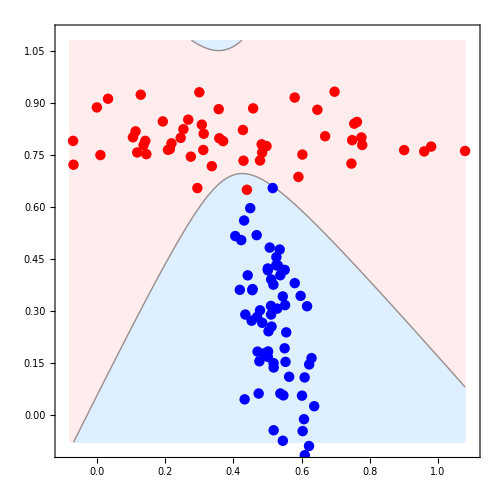

```mathematica
MakeGaussPlot[GaussDataSet,55/120,pmu1,pSigma1,65/120,nmu1,nSigma1]
```

Plot data set together with discriminant function using estimated distribution parameters:

Negative class: no. of samples=65 mu={0.524475,0.241031} Sigma={{0.003604,-0.00661103},{-0.00661103,0.0398028}}

Positive class: no. of samples=55 mu={0.413013,0.796972} Sigma={{0.0980913,-0.000584099},{-0.000584099,0.00422907}}

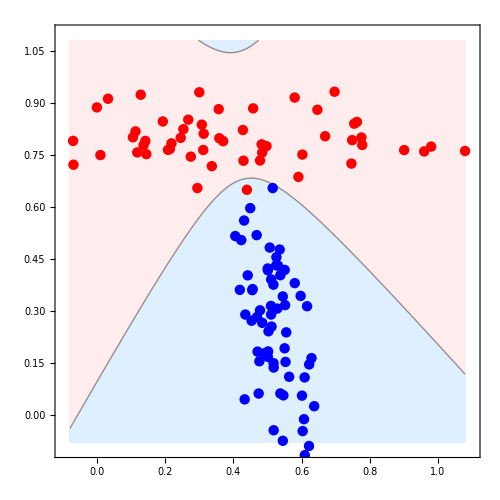

```mathematica
MakeGaussPlotEstimates[GaussDataSet]
```

```mathematica
Plot data set together with KNN discriminant function using k=1, k=5  and k=11 (using the whole data set as training set):
```

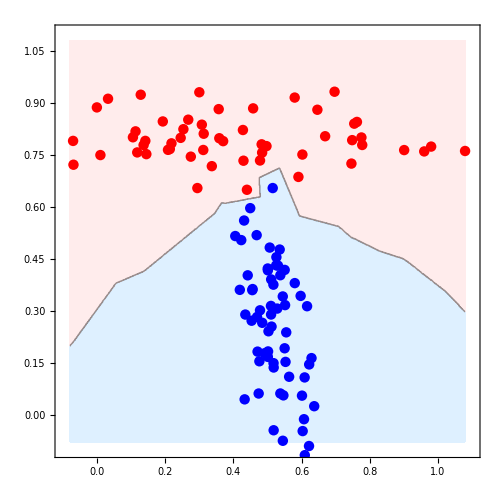

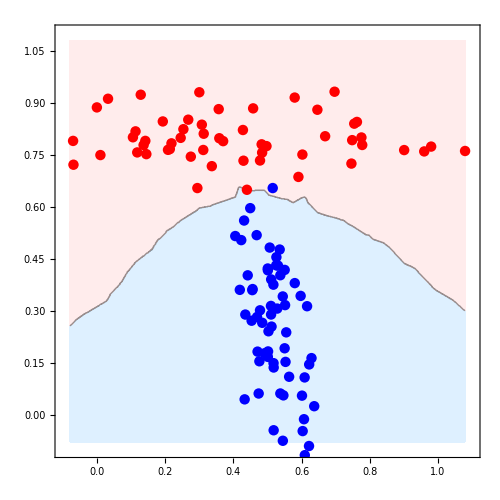

```mathematica
ShowClassification[{ClassificationFunctionPlot[KNN[{#1,#2},GaussDataSet,1]&],ClassificationDataPlot[GaussDataSet]}]
ShowClassification[{ClassificationFunctionPlot[KNN[{#1,#2},GaussDataSet,5]&],ClassificationDataPlot[GaussDataSet]}]
```

## Example 2

#### Plot data set loaded from file together with discriminant function using estimated distribution parameters:

Negative class: no. of samples=65 mu={0.507401,0.273295} Sigma={{0.00490593,-0.00689359},{-0.00689359,0.0320171}}

Positive class: no. of samples=55 mu={0.45187,0.808593} Sigma={{0.0813118,-0.000346911},{-0.000346911,0.00554746}}

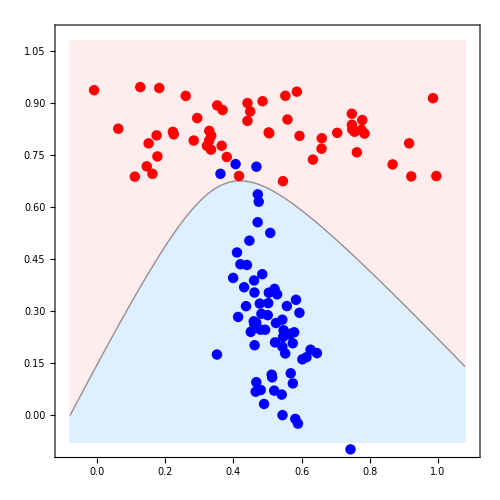

```mathematica
MakeGaussPlotEstimates[DataSet6]
```